```mathematica
Clear["Global`*"]
```

```mathematica
inputData = Import[NotebookDirectory[]<>"/input.txt"];
input = StringSplit[inputData];
l=Length[input];(*l will have to be even*)
(*Write a function here that will take in strings as variable names*)
dt=Read[StringToStream[input[[2]]]];
tmax=input[[4]];
nTrajectory=input[[6]];
nstore=input[[8]];
yWall=input[[10]];
sigmaXX=input[[12]];
sigmaXZ=input[[14]];
transitTime=input[[16]];
sigmaPX=input[[18]];
sigmaPY=input[[20]];
sigmaPZ=input[[22]];
density=input[[24]];
rabi=input[[26]];
kappa=input[[28]];
name =input[[30]]
```

tau5_dens10_g1.4_k20

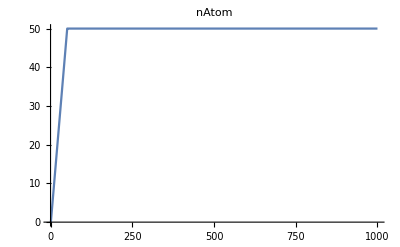

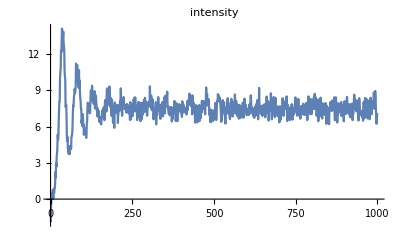

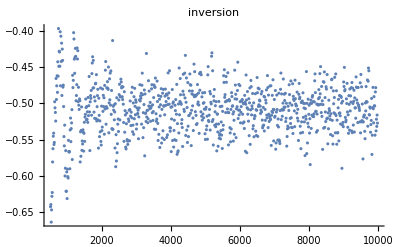

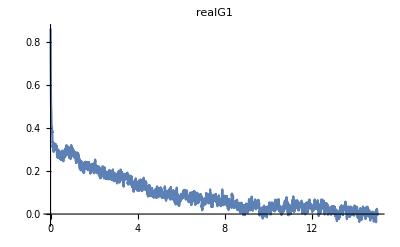

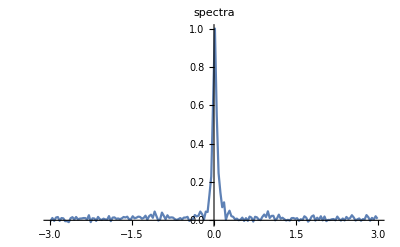

```mathematica
(*When doing one run*)
intensity=Flatten[Import[NotebookDirectory[]<>name<>"/intensity.dat"]];
nAtom=Flatten[Import[NotebookDirectory[]<>name<>"/nAtom.dat"]];
inversionAve=Flatten[Import[NotebookDirectory[]<>name<>"/inversionAve.dat"]];
szFinal=Flatten[Import[NotebookDirectory[]<>name<>"/szFinal.dat"]];
realG1 = Import[NotebookDirectory[]<>name<>"/realG1.dat"];
spectra=Import[NotebookDirectory[]<>name<>"/spectra.dat"];
ListLinePlot[nAtom,PlotRange->All,PlotLabel->"nAtom"]
ListLinePlot[intensity,PlotRange->All,PlotLabel->"intensity"]
ListPlot[szFinal,PlotRange->All,PlotLabel->"inversion"]
ListLinePlot[realG1,PlotRange->All,PlotLabel->"realG1"]
ListLinePlot[spectra,PlotRange->All,PlotLabel->"spectra"]
```

FittedModel[0.0016378/(0.0017461+x^2)]

| Estimate | Standard Error | t-Statistic | P-Value
linewidth | 0.0835728 | 0.00431075 | 19.3871 | 9.63969×10^-46
A | 0.0391946 | 0.00133793 | 29.2949 | 5.36857×10^-70

0.0835728

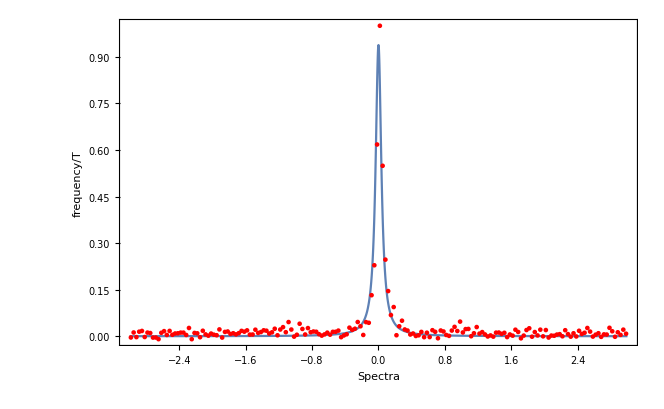

```mathematica
(*Fit the spectra to lorentzian*)
lorentzianModel=A(1/2 linewidth)/(x^2+(1/2 linewidth)^2);
fitLoren=NonlinearModelFit[spectra,{lorentzianModel},{linewidth,A},{x}]
fitLoren["ParameterTable"]
linewidth1 = linewidth/.fitLoren["BestFitParameters"]
Show[{Plot[fitLoren[x],{x,-3,3},PlotRange->All,BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.005],Map[Point,spectra]}]},Frame->True,FrameLabel->{"Spectra","frequency/T"}]
```

B ⅇ^(-t/tc)

FittedModel[0.342129 ⅇ^(-0.235082 t)]

| Estimate | Standard Error | t-Statistic | P-Value
tc | 4.25384 | 0.0180649 | 235.476 | 3.4718050907×10^-3467
B | 0.342129 | 0.00101284 | 337.791 | 2.0836262431×10^-4539

4.25384

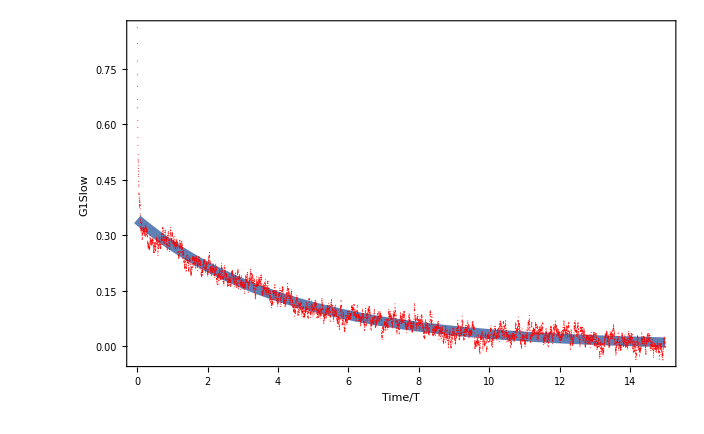

```mathematica
(*Fit the G1 function to exponential*)
exponentialModel=B Exp[- t/tc]
fitExp=NonlinearModelFit[realG1,{exponentialModel},{tc,B},{t}]
fitExp["ParameterTable"]
tc=tc/.fitExp["BestFitParameters"]
Show[{Plot[fitExp[x],{x,0,Last[realG1][[1]]},PlotRange->All,PlotStyle->{Thickness[0.01]},BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.001],Map[Point,realG1]}]},Frame->True,FrameLabel->{"Time/T","G1Slow"}]
```

```mathematica
(*Get the linewidth form the coherent time*)
linewidth2 = 1/(tc Pi)
```

0.0748288

```mathematica
(*Notice there is another exponential decay.*)
```

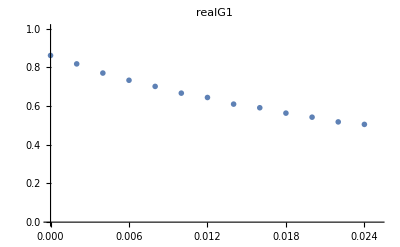

B2 ⅇ^(-d π t)

FittedModel[0.850233 ⅇ^(-23.0729 t)]

| Estimate | Standard Error | t-Statistic | P-Value
d | 7.34434 | 0.138035 | 53.2062 | 1.33185×10^-13
B2 | 0.850233 | 0.00409052 | 207.855 | 1.63319×10^-19

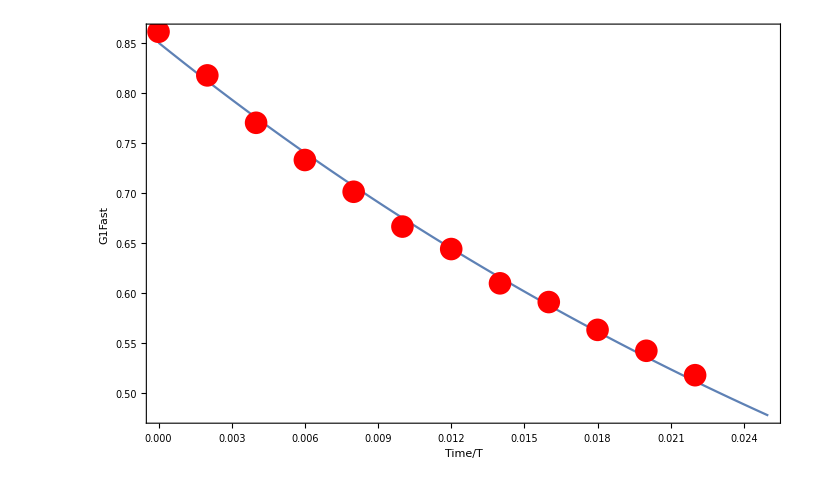

```mathematica
cutOff = 0.025;
ListPlot[realG1,PlotRange->{{0,cutOff},{0,1}}, 
PlotLabel->"realG1",PlotMarkers->{Automatic,Small}]
secondNum=IntegerPart[cutOff/realG1[[2,1]]];
secondExp=Take[realG1,secondNum];
exponentialModel2=B2 Exp[- d Pi t]
fitExp2=NonlinearModelFit[secondExp,{exponentialModel2},{d,B2},{t}]
fitExp2["ParameterTable"]
Show[{Plot[fitExp2[x],{x,0,cutOff},PlotRange->All,BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.02],Map[Point,secondExp]}]},Frame->True,FrameLabel->{"Time/T","G1Fast"}]
```

```mathematica
secondTc = 1/(d Pi)/.fitExp2["BestFitParameters"]
```

0.0433409